### Basic Examples (2)

The hydrogen ground state wavefunction:

```mathematica
[{1,0,0},a,{r,θ,ϕ}]
```

(√(1/a^3) ⅇ^(-r/a))/(√π)

The squared magnitude of the wavefunction gives the probability distribution for finding the electron:

```mathematica
Simplify[Abs[[{3,1,-1},a,{r,θ,ϕ}]]^2,a>0&&r>0&&0<ϕ<π&&0<θ<2π]
```

(ⅇ^(-(2 r)/(3 a)) r^2 (-6 a+r)^2 Sin[θ]^2)/(6561 a^7 π)

### Scope (3)

Plot radial dependence of a few wavefunctions:

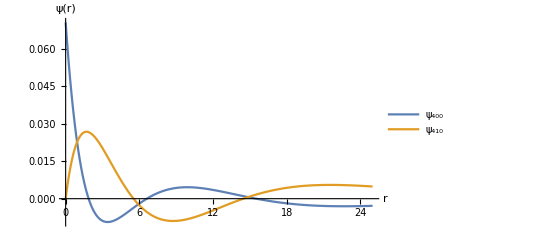

```mathematica
With[{a=1},Plot[Evaluate[Re/@{[{4,0,0},a,{r,0,ϕ}],[{4,1,0},a,{r,0,ϕ}]}],{r,0,25},]]
```

Plot the polar dependence of one wavefunction at various radii:

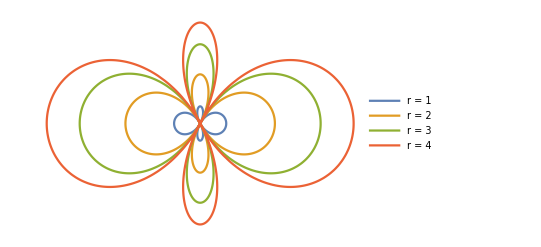

```mathematica
With[{a=1},PolarPlot[Evaluate[Table[Re@[{3,2,0},a,{r,θ,0}],{r,4}]],{θ,0,2π},]]
```

Plot the electron probability density for various wavefunctions:

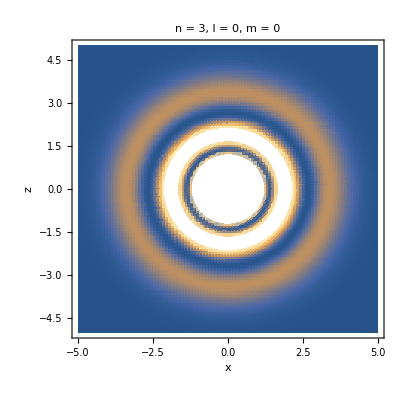
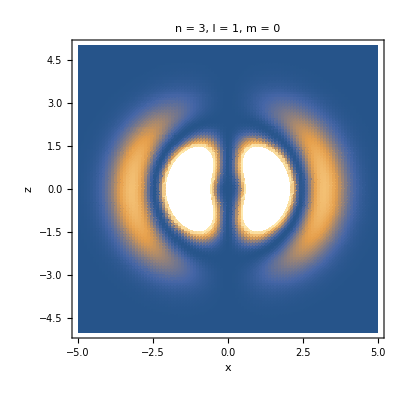
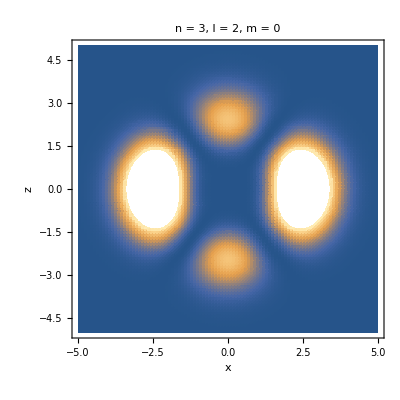

```mathematica
With[{a=1},Table[DensityPlot[Abs[[{3,l,0},a,{x^2+y^2,ArcTan[x,y],0}]]^2,{x,-5,5},{y,-5,5},],{l,0,2}]]
```

### Properties and Relations (4)

Verify the orthogonality property of HydrogenWavefunction:

```mathematica
Assuming[a>0,∫_0^(2π) ∫_0^π ∫_0^∞ Conjugate[[{3,2,1},a,{r,θ,ϕ}]][{3,2,-1},a,{r,θ,ϕ}] r^2 Sin[θ]ⅆrⅆθⅆϕ]
```

0

Verify the normalization property of HydrogenWavefunction:

```mathematica
Assuming[a>0,∫_0^(2π) ∫_0^π ∫_0^∞ Abs[[{3,2,0},a,{r,θ,ϕ}]]^2 r^2 Sin[θ]ⅆrⅆθⅆϕ]
```

1

Verify that HydrogenWavefunction satisfies the time-independent Schrödinger equation:

```mathematica
With[{n=3,l=2,m=-1},
ψ=[{n,l,m},a,{r,θ,ϕ}];Simplify[-ℏ^2/(2μ)Laplacian[ψ,{r,θ,ϕ},"Spherical"]-ℯ^2/(4π Subscript[ε, 0] r)ψ==-ℏ^2/(2μ a^2 n^2)ψ/.a->(4π Subscript[ε, 0] ℏ^2)/(μ ℯ^2)]]
```

True

Show a change of nuclear charge:

```mathematica
Grid[{#,[{1,0,0},a,{r,θ,ϕ},#]}&/@{1,2}, Frame-> All]
```

1 | (√(1/a^3) ⅇ^(-r/a))/(√π)
2 | 2 √(1/a^3) ⅇ^(-(2 r)/a) √(2/π)

### Neat Examples (1)

Plot hydrogen orbital densities:

```mathematica
With[{a0=Quantity["BohrRadius"]/Quantity["Meters"],n=2,l=1,m=0},DensityPlot3D[Abs[[{n,l,m},a0,{√(x^2+y^2+z^2),ArcTan[z,√(x^2+y^2)],ArcTan[x,y]}]]^2,{x,-5 a0,5 a0},{y,-5 a0,5 a0},{z,-5 a0,5 a0},PlotLegends->Automatic]]
```

-Graphics3D-

-Graphics3D-